## Nucleation Analysis (Multi - stranded)

```mathematica
Needs["PlotLegends`"]
PartitionFunctionFILE="PartitionFunction_0_0.out";
FreeEnergyFileFILE="FreeEnergy_0_0.out";
PotentialDataFILE="POTENTIAL_DATA";
ParametersFILE="Parameters";

CollagenAnalyticalPATH="collagen_analytical/results/";

SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

FrameBox["Analytical Parameters"]//DisplayForm
PartitionFunctionCollagenAnalytical=Import[CollagenAnalyticalPATH<>PartitionFunctionFILE,"Table"];
FreeEnergyCollagenAnalytical=Import[CollagenAnalyticalPATH<>FreeEnergyFileFILE,"Table"];
PotentialCollagenAnalytical=Import[CollagenAnalyticalPATH<>PotentialDataFILE,"Table"];
ParametersCollagenAnalytical=Import[CollagenAnalyticalPATH<>ParametersFILE,"Grid"]
Print["\n"]

L=IntegerPart[ParametersCollagenAnalytical[[1,2]][[2]]];
m=IntegerPart[ParametersCollagenAnalytical[[1,3]][[2]]];
n=IntegerPart[ParametersCollagenAnalytical[[1,4]][[2]]];
kappa=IntegerPart[ParametersCollagenAnalytical[[1,5]][[2]]];
sigma=IntegerPart[ParametersCollagenAnalytical[[1,6]][[2]]];

Needs["PlotLegends`"]
```

/Users/htailor/Desktop/collagen_code

Analytical Parameters

| 
L: | 5.
m: | 20
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20
 | 
 | 
beta: | 4.
mu: | 6.
c: | 4.58
delta: | 19.17
b: | 2.14
k: | 1.57
ev0: | 0.81
C0: | 0.55

Results - Free Energy

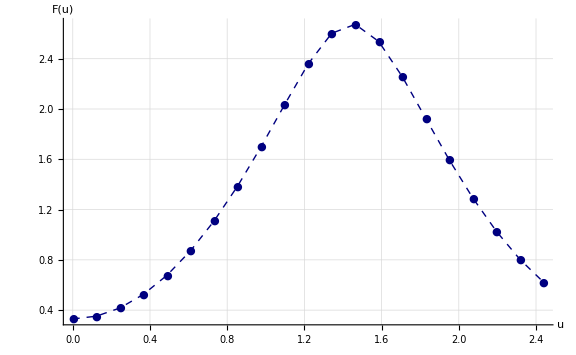

```mathematica
fsAxesLabel=24;
fs2=18;

plot=ListLinePlot[
{
FreeEnergyCollagenAnalytical
},
PlotRange->All,
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["F(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,Dashed,Darker[Blue,0.5]}
},
PlotMarkers->{"●"},
PlotRange->All
]
```

```mathematica
Export["./col_analytical_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",plot]
```

./col_analytical_N5_L5_m10_kappa1_sigma1.pdf